Problem-8a::-

```mathematica
sol1=NDSolve[{y''[x]==-Exp[-2*y[x]], y[1]==0,y[2]==Log[2]},y[x],{x,1,2}]
```

{{y[x]→InterpolatingFunction[…][x]}}

InterpolatingFunction[…][x]

{0.,0.0100503,0.0200007,0.0298529,0.0396091,0.049271,0.0588405,0.0683192,0.077709,0.0870114,0.096228,0.105361,0.11441,0.123379,0.132268,0.141079,0.149812,0.15847,0.167054,0.175565,0.184004,0.192372,0.200671,0.208901,0.217064,0.225162,0.233194,0.241162,0.249067,0.25691,0.264693,0.272415,0.280077,0.287682,0.295229,0.30272,0.310155,0.317535,0.324861,0.332134,0.339354,0.346523,0.35364,0.360707,0.367725,0.374693,0.381614,0.388487,0.395313,0.402092,0.408826,0.415515,0.42216,0.428761,0.435318,0.441833,0.448305,0.454736,0.461126,0.467475,0.473784,0.480054,0.486285,0.492476,0.49863,0.504747,0.510826,0.516868,0.522874,0.528844,0.534779,0.540679,0.546544,0.552375,0.558172,0.563935,0.569666,0.575364,0.58103,0.586664,0.592266,0.597837,0.603377,0.608887,0.614366,0.619816,0.625236,0.630627,0.635989,0.641322,0.646627,0.651904,0.657154,0.662376,0.66757,0.672738,0.67788,0.682995,0.688084,0.693147}

txt file of problem 8a.txt

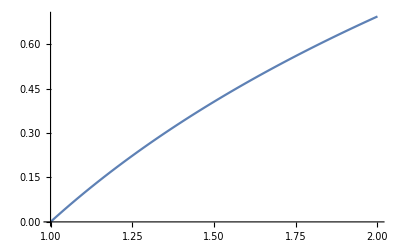

```mathematica
f1[x_]=y[x]/.sol1[[1]]
t1= Table[f1[x],{x,1,2,(2-1)/99}]
Export["txt file of problem 8a.txt",t1,"Table"]
Plot[y[x]/.sol1,{x,1,2}]
```

Problem-8b::-

{{y[x]→InterpolatingFunction[…][x]}}

InterpolatingFunction[…][x]

{1.,1.01599,1.03224,1.04873,1.06548,1.08247,1.09972,1.11721,1.13495,1.15294,1.17117,1.18964,1.20834,1.22729,1.24646,1.26587,1.2855,1.30535,1.32542,1.34571,1.3662,1.3869,1.40779,1.42887,1.45014,1.47159,1.49321,1.515,1.53694,1.55903,1.58127,1.60363,1.62612,1.64872,1.67143,1.69423,1.71711,1.74006,1.76308,1.78614,1.80924,1.83237,1.85551,1.87865,1.90177,1.92487,1.94793,1.97094,1.99387,2.01672,2.03948,2.06212,2.08463,2.107,2.12921,2.15124,2.17308,2.19472,2.21613,2.2373,2.25822,2.27886,2.29922,2.31927,2.339,2.3584,2.37744,2.39612,2.41441,2.4323,2.44977,2.46681,2.48341,2.49954,2.5152,2.53038,2.54504,2.55919,2.57282,2.58589,2.59842,2.61037,2.62175,2.63254,2.64273,2.65231,2.66127,2.6696,2.6773,2.68435,2.69075,2.6965,2.70158,2.706,2.70975,2.71281,2.7152,2.71691,2.71794,2.71828}

txt file of problem 8b.txt

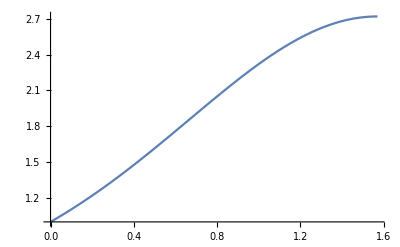

```mathematica
sol2=NDSolve[{y''[x]==y'[x]*Cos[x] - y[x]*Log[y[x]], y[0]==1,y[Pi/2]==Exp[1]},y[x],{x,0,Pi/2}]
f2[x_]=y[x]/.sol2[[1]]
t2= Table[f2[x],{x,0,Pi/2,(Pi/2-0)/99}]
Export["txt file of problem 8b.txt",t2,"Table"]
Plot[y[x]/.sol2,{x,0,Pi/2}]
```

Problem-8c::-

{{y[x]→InterpolatingFunction[…][x]}}

InterpolatingFunction[…][x]

{0.840896,0.842006,0.843111,0.844212,0.845309,0.846401,0.847488,0.848572,0.849651,0.850726,0.851796,0.852862,0.853924,0.854981,0.856034,0.857083,0.858128,0.859168,0.860204,0.861236,0.862264,0.863287,0.864306,0.865321,0.866332,0.867338,0.86834,0.869339,0.870332,0.871322,0.872308,0.873289,0.874267,0.87524,0.876209,0.877173,0.878134,0.879091,0.880043,0.880992,0.881936,0.882876,0.883812,0.884744,0.885672,0.886596,0.887516,0.888432,0.889344,0.890251,0.891155,0.892055,0.89295,0.893842,0.89473,0.895613,0.896493,0.897369,0.89824,0.899108,0.899971,0.900831,0.901687,0.902539,0.903386,0.90423,0.90507,0.905906,0.906738,0.907566,0.90839,0.909211,0.910027,0.91084,0.911648,0.912453,0.913253,0.91405,0.914843,0.915632,0.916417,0.917199,0.917976,0.91875,0.919519,0.920285,0.921047,0.921806,0.92256,0.92331,0.924057,0.9248,0.925539,0.926274,0.927005,0.927733,0.928457,0.929176,0.929893,0.930605}

txt file of problem 8c.txt

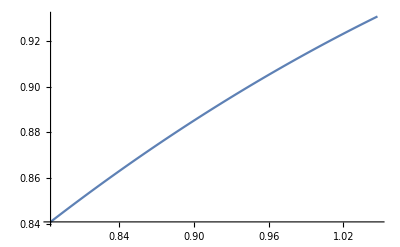

```mathematica
sol3=NDSolve[{y''[x]==- Sec[x]*(2*(y'[x])^3+ (y'[x] * y[x]^2)), y[Pi/4]==2^(-1/4),y[Pi/3]==12^(1/4)/2},y[x],{x,Pi/4,Pi/3}]
f3[x_]=y[x]/.sol3[[1]]
t3= Table[f3[x],{x,Pi/4,Pi/3,(Pi/3-Pi/4)/99}]
Export["txt file of problem 8c.txt",t3,"Table"]
Plot[y[x]/.sol3,{x,Pi/4,Pi/3}]
```

Problem-8d::-

{{y[x]→InterpolatingFunction[…][x]}}

InterpolatingFunction[…][x]

{2.,2.03173,2.06342,2.09506,2.12659,2.158,2.18925,2.22031,2.25115,2.28173,2.31203,2.34202,2.37166,2.40093,2.42979,2.45823,2.4862,2.51368,2.54064,2.56706,2.59291,2.61816,2.64279,2.66677,2.69008,2.71269,2.73459,2.75575,2.77615,2.79576,2.81458,2.83257,2.84973,2.86603,2.88145,2.89599,2.90963,2.92235,2.93415,2.945,2.9549,2.96384,2.97181,2.9788,2.98481,2.98982,2.99384,2.99685,2.99887,2.99987,2.99987,2.99887,2.99685,2.99384,2.98982,2.98481,2.9788,2.97181,2.96384,2.9549,2.945,2.93415,2.92235,2.90963,2.89599,2.88145,2.86603,2.84973,2.83257,2.81458,2.79576,2.77615,2.75575,2.73459,2.71269,2.69008,2.66677,2.64279,2.61816,2.59291,2.56706,2.54064,2.51368,2.4862,2.45823,2.42979,2.40093,2.37166,2.34202,2.31203,2.28173,2.25115,2.22031,2.18925,2.158,2.12659,2.09506,2.06342,2.03173,2.}

txt file of problem 8d.txt

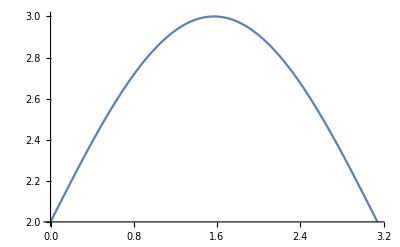

```mathematica
sol4=NDSolve[{y''[x]== 1/2 - (y'[x])^2/2 - y[x]* Sin[x]/2, y[0]==2,y[Pi]==2},y[x],{x,0,Pi}]
f4[x_]=y[x]/.sol4[[1]]
t4= Table[f4[x],{x,0,Pi,(Pi-0)/99}]
Export["txt file of problem 8d.txt",t4,"Table"]
Plot[y[x]/.sol4,{x,0,Pi}]
```